```mathematica
T = 
{
{1/2, 1, 1/2},
{3/2,0,1/2},
{3/2, -1,3/2}
}
```

{{1/2,1,1/2},{3/2,0,1/2},{3/2,-1,3/2}}

```mathematica
A = 
{
{1,-1,1},
{1,1,1},
{-1,1,1}
}
```

{{1,-1,1},{1,1,1},{-1,1,1}}

```mathematica
MatrixForm[Dot[Inverse[A], T, A]]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 2)

```mathematica
Tr[T]
```

2

```mathematica
Det[T]
```

-2

0.667986

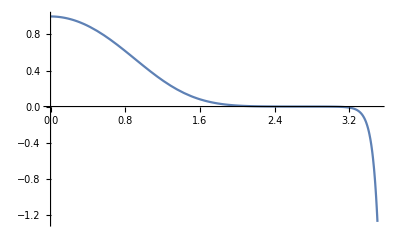

```mathematica
Clear[e,psi];
e=0.66798636
psi=psi/. NDSolve[{-(1/2) psi''[u]+(u^4-e) psi[u]==0,psi[0]==1,psi'[0]==0},psi,{u,0,3.5}][[1]];
Plot[psi[u],{u,0,3.5}]
```

```mathematica
E2 = 2.39364
E2-(epsilon_1)^2*(E_2-E_1)+(epsilon_3)^2*(E_3-E_2)+(epsilon_4)^2*(E_4-E_2)
```

```mathematica
Cos[t/2]^2*Cos[t2/2]^2+Sin[t/2]^2*Sin[t2/2]^2+2*Cos[p-p2]*Cos[t/2]*Cos[t2/2]*Sin[t/2]*Sin[t2/2] - Cos[t/2]*Cos[t2/2]+Sin[t/2]*Sin[t2/2]*(Cos[p-p2]+I*Sin[p-p2]) //Simplify
```

-Cos[t/2] Cos[t2/2]+Cos[t/2]^2 Cos[t2/2]^2+(Cos[p-p2]+ⅈ Sin[p-p2]) Sin[t/2] Sin[t2/2]+Sin[t/2]^2 Sin[t2/2]^2+1/2 Cos[p-p2] Sin[t] Sin[t2]